## Eli — PS 7 — 2025-02-11

## EIWL3 Sections 18 and 19

## I had repeated issues with timeouts when downloading GeoGraphics. Because of that, I did not re-execute your PS7 notebooks like I usually do (to check for errors upon re-execution). Instead, I just PDF’d them the way that you gave them to me.

## Chap 18

```mathematica
GeoDistance[,]
```

3453.71 mi

```mathematica
GeoDistance[,]/GeoDistance[,]
```

1.35109

```mathematica
UnitConvert[GeoDistance[,],]
```

14387. km

```mathematica
GeoGraphics[]
```

-Graphics-

```mathematica
GeoListPlot[{,,,}]
```

-Graphics-

```mathematica
GeoGraphics[GeoPath[]]
```

-Graphics-

```mathematica
GeoGraphics[GeoDisk[,]]
```

-Graphics-

```mathematica
GeoGraphics[GeoDisk[,GeoDistance[]]]
```

-Graphics-

```mathematica
GeoImage[GeoDisk[,]]
```

-Graphics-

```mathematica
GeoNearest["Country", ,5]
```

{Greenland,Canada,Russia,Svalbard,United States}


{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[GeoNearest["Country",GeoPosition[{45,0}],3][[n]]["Flag"],{n,1,3}] (*how to get the flag of them not individually?*)
```

```mathematica
GeoListPlot[GeoNearest["Volcano",,25]]
```

-Graphics-

```mathematica
["Position"][[1,1]]-["Position"][[1,1]]
```

6.64488

## Chapter 19

```mathematica
Length[DayRange[,]]
```

45698

```mathematica
DayName[]
```

Saturday

```mathematica
DateObject[-]
```

April 29, 1751 7:38 amGMT-6

```mathematica
LocalTime[]
```

February 11, 2025 7:08 pmGMT+5.5

```mathematica
Sunset[,]-Sunrise[,]
```

10.12 h

```mathematica
MoonPhase[,"Icon"]
```

-Graphics-

```mathematica
Table[MoonPhase[+n ],{n,1,10}]
```

{0.998115,0.99507,0.972393,0.931991,0.876155,0.807337,0.727997,0.640555,0.547426,0.451159}

```mathematica
Table[MoonPhase[+n ,"Icon"],{n,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Sunrise[,]- Sunrise[,]
```

4.54772 h

```mathematica
N[Length[DayRange[["Date"],]]/365]
```

55.6055

```mathematica
AirTemperatureData[,]
```

42.8 °F

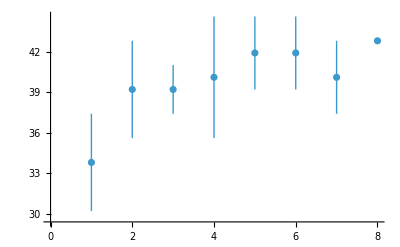

```mathematica
ListPlot[AirTemperatureData[,DayRange[,]]]
```

```mathematica
AirTemperatureData[,]-AirTemperatureData[,]
```

-20. _Δ^◦F

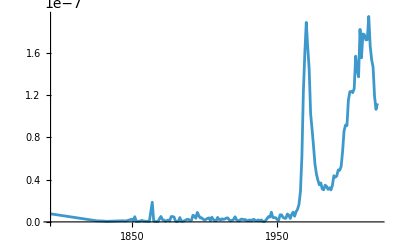

```mathematica
ListLinePlot[WordFrequencyData["groovy","TimeSeries"]]
```

```mathematica
[Dated["Population",2000]]-[Dated["Population",1900]]
```

20759628 people